# Monty Hall Problem

The Monty Hall Problem is an absurdly counter-intuitive statistics puzzle that gained popularity after being featured in a Parade magazine column

## History of the problem

This problem is loosely based on a TV game show called “Let’s Make A Deal” and is named after its host. It was originally proposed and solved in a 1975 issue of American Statistician. In 1990, a reader posed the same question to a weekly column in Parade magazine. The published response (which was correct) gained fame as nearly 1000 mathematics PhDs wrote letters claiming it was wrong and lamented about the state of school education in America.

## The Question

Suppose you’re on a game show, and you’re given the choice of three doors: Behind one door is a car; behind the others, goats. You pick a door, say No. 1, and the host, who knows what’s behind the doors, opens another door, say No. 3, which has a goat. He then says to you, “Do you want to pick door No. 2?” Is it to your advantage to switch your choice?

```mathematica
Import["https://upload.wikimedia.org/wikipedia/commons/thumb/3/3f/Monty_open_door.svg/1280px-Monty_open_door.svg.png"]
```

-Graphics-

## Interactive Demo

This demo (inspired by this) allows you to choose a door and have the host immediately open another door containing a goat. You can then hover around to check what is behind the other doors.

Creates an interactive version of the game. The parameter seed will be used to seed the pseudorandom generator and can be altered to shuffle.

```mathematica
MHDemo[seed_]:=Module[{},
Goat=
ImageCrop[
Import[
"http://img.stockfresh.com/files/k/kiddaikiddee/x/53/6249071_69000897.jpg"]];
Car=ImageCrop[Import["https://geoexpat.com/components/com_djclassifieds/images/category/x19_clsf_icon_cars_v2_ths.gif.pagespeed.gp+jp+pj+js+rj+rp+rw+ri+cp+md.ic.9c3BvwuhXU.png"]];
Manipulate[SeedRandom[seed];
Doors={1,2,3};
var1=Random[Integer,{1,3}];var2=If[var1==Choice, {Complement[Doors,{var1,Choice}][[Random[Integer,{0,1}]]]},Complement[Doors,{var1,Choice}] ];

StateReset=Graphics[{
Brown,
Rectangle[{0,0},{1,2}],
Rectangle[{1.5, 0},{2.5,2}], 
Rectangle[{3,0},{4,2}],
White,
Style[Text["Door 1", {.5,1.5}],24],
Style[Text["Door 2", {2,1.5}],24],
Style[Text["Door 3", {3.5,1.5}],24]}];

State1=Graphics[{
Style[Text["Goat",{.5,1}], 40],
Brown,
Tooltip[Rectangle[{1.5, 0},{2.5,2}],If[var1==2, Style[Car, 30],Style[Goat, 30]]], 
Tooltip[Rectangle[{3,0},{4,2}],If[var1==3, Style[Car, 30],Style[Goat, 30]]],
White,
Style[Text["Door 2", {2,1.5}],24],
Style[Text["Door 3", {3.5,1.5}],24]
}];

State2=Graphics[{
Style[Text["Goat",{2,1}],40],
Brown,
Tooltip[Rectangle[{0, 0},{1,2}],If[var1==1, Style[Car, 30],Style[Goat, 30]]], 
Tooltip[Rectangle[{3,0},{4,2}],If[var1==3, Style[Car, 30],Style[Goat, 30]]],
White,
Style[Text["Door 1", {.5,1.5}],24],
Style[Text["Door 3", {3.5,1.5}],24]}];

State3=Graphics[{
Style[Text["Goat",{3.5,1}],40],
Brown,
Tooltip[Rectangle[{0, 0},{1,2}],If[var1==1,Style[Car, 30],Style[Goat, 30]]], 
Tooltip[Rectangle[{1.5,0},{2.5,2}],If[var1==2, Style[Car, 30],Style[Goat, 30]]],
White,
Style[Text["Door 1", {.5,1.5}],24],
Style[Text["Door 2", {2,1.5}],24]}];

Which[Choice==0,StateReset,var2=={1}, State1, var2=={2}, State2,var2=={3}, State3],

{{Choice,0,"Door No. :"},{0->"Reset",1->"1",2->"2",3->"3"}, ControlType->RadioButtonBar}
]];
```

```mathematica
MHDemo["MontyHall"]
```

## Simulation

This problem is classified as a veridical paradox as the solution is so counter-intuitive, it actually sounds absurd. Paul Erdős himself took days to understand the solution and finally conceded only after being shown a computer simulation.

Let’s run the simulation here:

```mathematica
MHSimulation[n_]:=Module[
{Choice,Car,Switch,NotSwitch},
Choice=RandomInteger[{1,3},n];
Car=RandomInteger[{1,3},n];
NotSwitch=Total[Boole[MapThread[SameQ,{Car,Choice}]]];
Switch=n- NotSwitch;
Grid[{{"Switch?","P(Winning)"},{"Yes",N[Switch/n]},{"No",N[NotSwitch/n]}},Frame->All]
]
```

```mathematica
MHSimulation[1000000]
```

Switch? | P(Winning)
Yes | 0.666675
No | 0.333325

## Graph/Plot

Finally, we can also plot Wins vs. Trials and calculate the probability of each choice (switch or not switch)

Plots a Graph of Wins vs Trials

```mathematica
MHPlot[n_]:=Module[
{Choice,Car,Switch,NotSwitch},
Choice=RandomInteger[{1,3},n];
Car=RandomInteger[{1,3},n];
NotSwitch=MapThread[SameQ,{Car,Choice}];
Switch=Boole@Map[Not,NotSwitch];
NotSwitch=Boole@NotSwitch;
Print["Probability of Switch (Red) Win :", N[Total[Switch]/n]];
Print["Probability of Non-Switch (Blue) Win :", N[Total[NotSwitch]/n]];
ListPlot[{Accumulate[NotSwitch], Accumulate[Switch]}, PlotRange->{{0,n},{0,2/3 n}},AxesLabel->{"Trials", "Wins"}]];
```

Probability of Switch (Red) Win :0.72

Probability of Non-Switch (Blue) Win :0.28

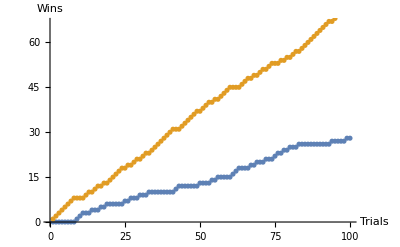

```mathematica
MHPlot[100]
```

Further Explorations

Bayes’ Theorem

Principle of restricted choice

Authorship information

Aditthya Ramakrishnan

23 June 2017
Waltham, MA

aditthya137@gmail.com